### Function Definitions

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
TestLifetime[rule_,init_List:{1},
max_Integer:100(*,infinity_:Infinity*)]:=With[
{array=CellularAutomaton[rule,{init,0},{max,All}]},If[#==0,-Infinity(*-infinity*),max-#+1]&[
LengthWhile[Reverse[array],Total[#]==0&]
]
]
```

```mathematica
ClearAll[AdaptiveSearch];Options[AdaptiveSearch] = {"MutationFunction"->RandomRuleMutation, "FitnessFunction"->TestLifetime,"SelectionFunction"->(#1>= #2&), "InitialFitness"->Automatic, "HaltCondition"->None};
AdaptiveSearch[sys_, steps_, OptionsPattern[AdaptiveSearch]]:=Module[{rule},
rule = First[sys];
NestList[
(Block[{newrule= OptionValue["MutationFunction"][#rule], newfitness},
newfitness = OptionValue["FitnessFunction"][newrule];
AssociationThread[{"rule", "fitness"}-> If[OptionValue["SelectionFunction"][newfitness, #fitness], {newrule, newfitness}, {#rule, #fitness}]]]
&),
<|"rule"-> rule, "fitness"-> If[OptionValue["InitialFitness"] === Automatic, OptionValue["FitnessFunction"][rule], OptionValue["InitialFitness"]]|>,
steps
]
]
```

### Sin growth rate

```mathematica
1 /
```

```mathematica
sf = Table[1/4Sin[(1/2.5)x], {x, 4Pi, 9Pi +  2/(2Pi), 1/(2Pi)}]+1/4;
```

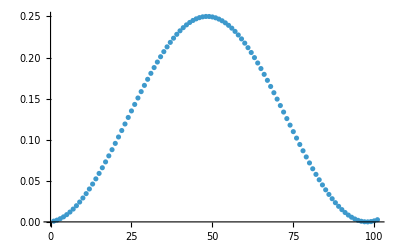

```mathematica
sf = Table[1/8Sin[(1/2.5)x], {x, 4Pi- 3/(2Pi), 9Pi - 1/(2Pi) , 1/(2Pi)}]+1/8;
ListPlot[sf]
```

```mathematica
SeedRandom[222344 + 3];AdaptiveSearch[CellularAutomaton[{0, 4, 1}], 6000, "FitnessFunction"-> (-Total[Abs[(Count[#, x_/;x>0] / 50&/@ CellularAutomaton[#, {{1}, 0}, {100, {-100, 100}}]) - sf]]&)]
```

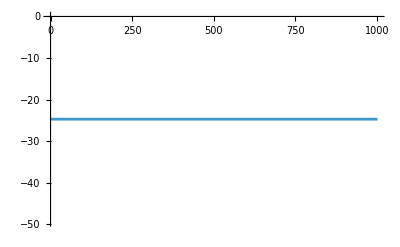

```mathematica
ListStepPlot[[[All, "fitness"]]]
```

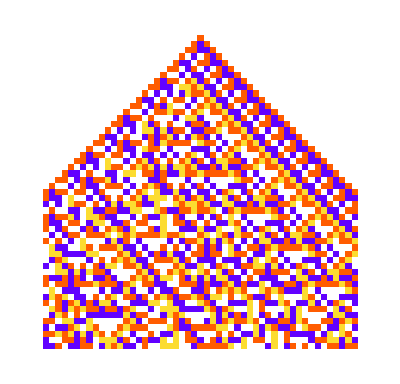

```mathematica
ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#rule, {{1}, 0}, {50,{-25, 25}}]]&[Last[]]
```

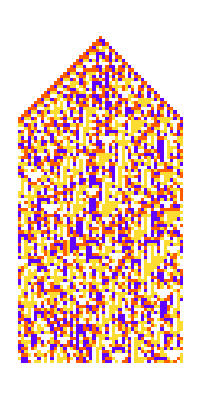
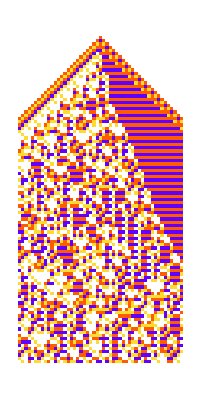
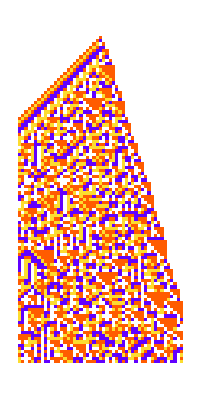
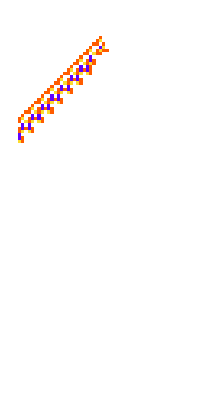
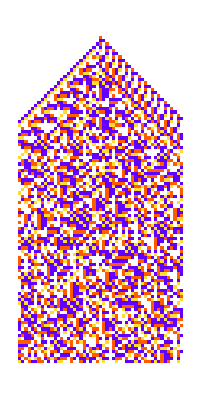
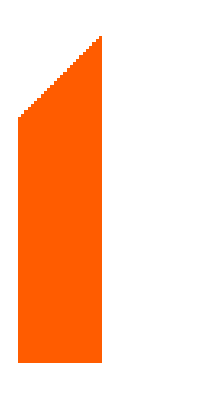
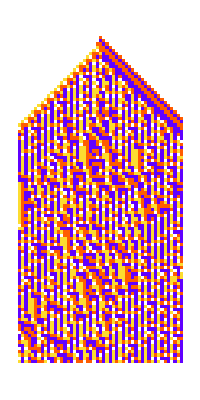
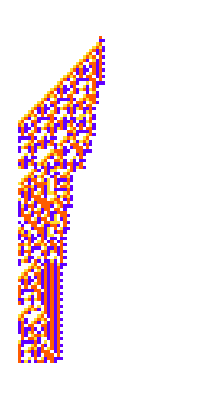
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[CellularAutomaton[#, {{1}, 0}, {100, {-25, 25}}]]&/@ [[1;;All;;100, "rule"]]
```

```mathematica
Last[]["rule"]
```

{293414014519514368983644874027306111636,4,1}

```mathematica
Count[{1, 2}, x_/;x>0]
```

2

```mathematica
Count[{1, 2}, x_/;x>0] / 50&/@ CellularAutomaton[Last[]["rule"], {{1}, 0}, {100, {-25, 25}}]
```

{1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25}

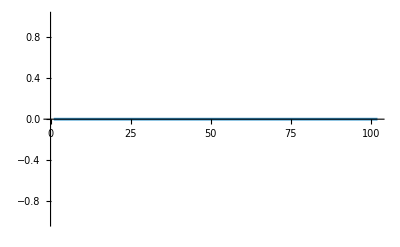
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListStepPlot/@(Count[#, x_/;x>0] / 50&/@ CellularAutomaton[#, {{1}, 0}, {100, {-25, 25}}]&)/@ [[1;;All;;100, "rule"]]
```

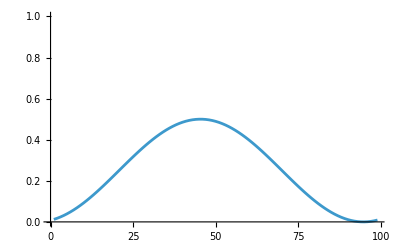

```mathematica
ListLinePlot[Table[1/4Sin[(1/2.5)x], {x, 4Pi, 9Pi, 1/(2Pi)}]+1/4, PlotRange->1]
```

```mathematica
{1, 2,3} - {9, 13, 11}
```

{-8,-11,-8}

```mathematica
-Total[Abs[(Count[#, 1||2||3] / 50&/@ CellularAutomaton[#, {{1}, 0}, {100, {-25, 25}}]) - sf]]&
```

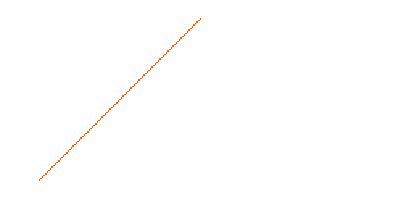
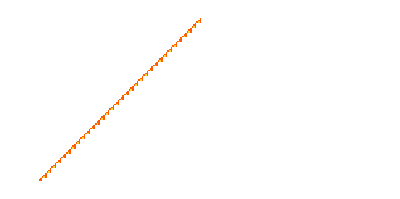
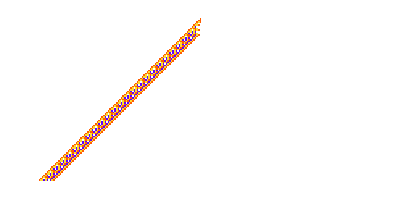
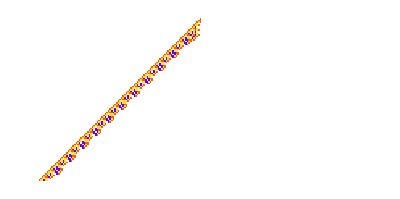
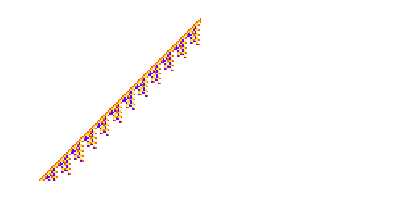
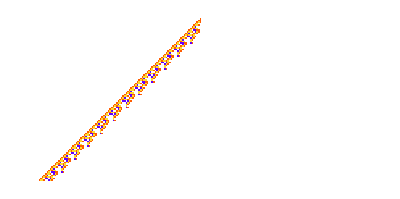
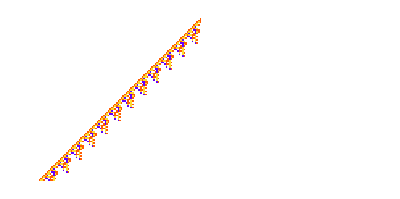
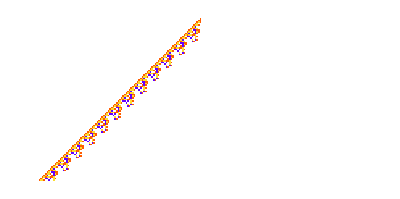
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[222344 + 8];ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#rule, {{1}, 0}, {100, {-100, 100}}], ImageSize->Automatic]&/@ GatherBy[, Last][[All, 1]]
```

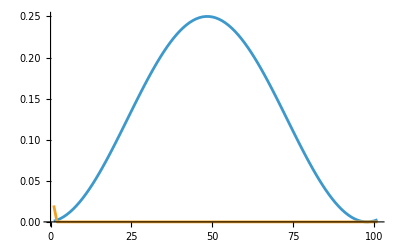
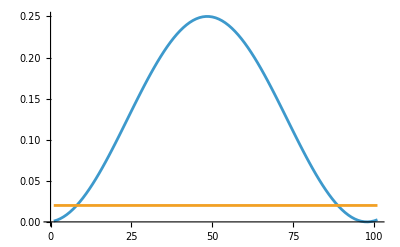
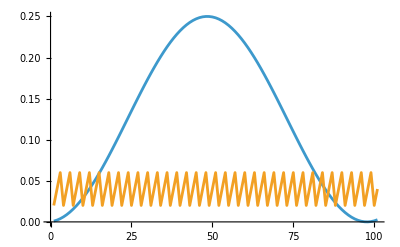
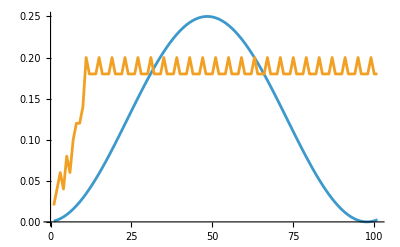
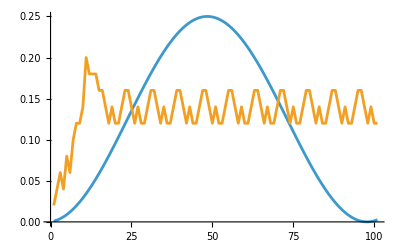
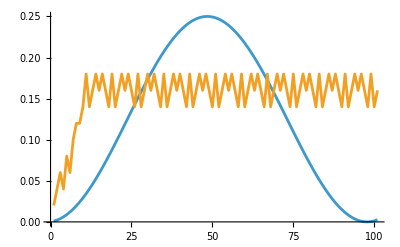
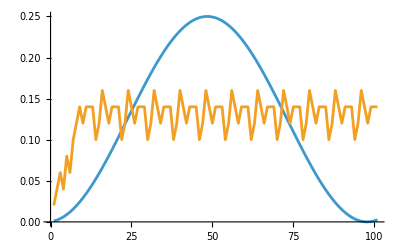
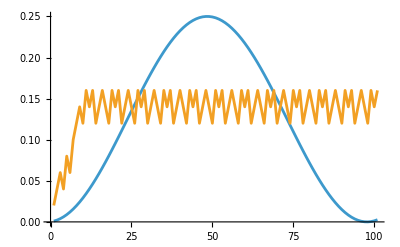

```mathematica
SeedRandom[222344 + 8];ListLinePlot[{sf, #}]&/@(Count[#, x_/;x>0] / 50&/@ CellularAutomaton[#rule, {{1}, 0}, {100, {-100, 100}}]&)/@ GatherBy[, Last][[All, 1]]
```

```mathematica
ByteCount[]
```

3409672

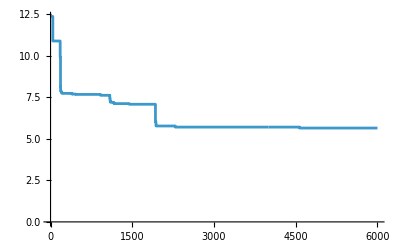

```mathematica
ListStepPlot[-[[All, "fitness"]]]
```

### More Runs

```mathematica
searches = ParallelTable[
SeedRandom[444110 + i];
AdaptiveSearch[CellularAutomaton[{0, 4, 1}], 2000,
"MutationFunction"->( RandomRuleMutation[#, 1, "Symmetric"->True]&),
 "FitnessFunction"-> (-Total[Abs[(Count[#, x_/;x>0] / 200&/@ CellularAutomaton[#, {{1}, 0}, {100, {-100, 100}}]) - sf]]&)], {i, 10}];
```

```mathematica
ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#rule, {{1}, 0}, {100, {-100, 100}}], ImageSize->Automatic]&/@ GatherBy[#, Last][[All, 1]]&/@ searches
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

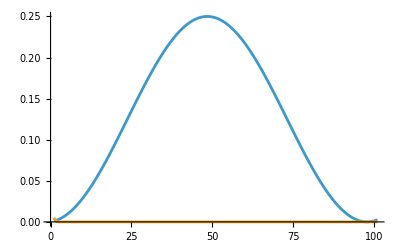
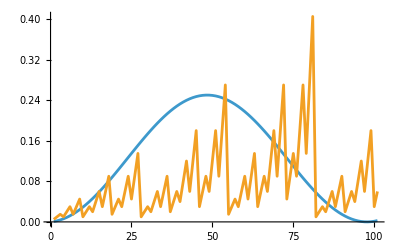
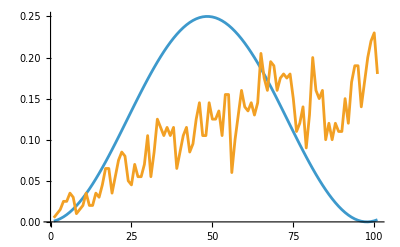
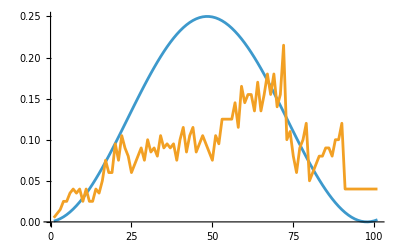
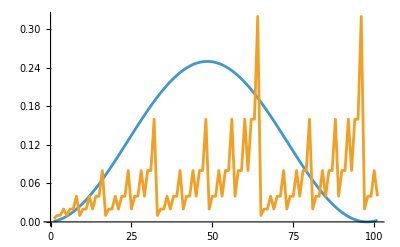
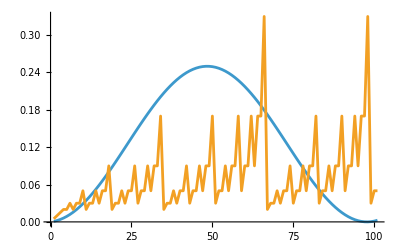
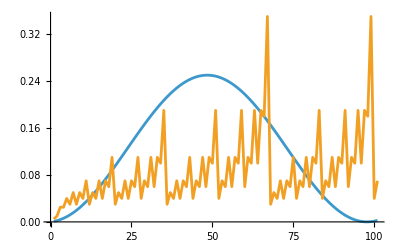
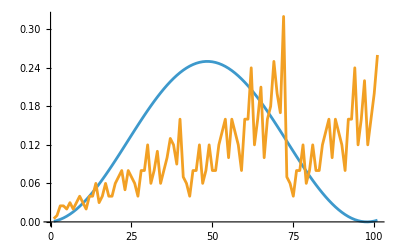
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
SeedRandom[222344 + 8];ListLinePlot[{sf, #}]&/@(Count[#, x_/;x>0] / 200&/@ CellularAutomaton[#rule, {{1}, 0}, {100, {-100, 100}}]&)/@ GatherBy[#, Last][[All, 1]]&/@ searches
```

### Zooming in on nice example

```mathematica
SeedRandom[444110 + 6];
exampleevolution = 
AdaptiveSearch[CellularAutomaton[{0, 4, 1}], 2000,
"MutationFunction"->( RandomRuleMutation[#, 1, "Symmetric"->True]&),
 "FitnessFunction"-> (-Total[Abs[(Count[#, x_/;x>0] / 200&/@ CellularAutomaton[#, {{1}, 0}, {100, {-100, 100}}]) - sf]]&)];
```

```mathematica
ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#rule, {{1}, 0}, {100, {-100, 100}}], ImageSize->Automatic]&/@ GatherBy[#, Last][[All, 1]]&@ exampleevolution
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[{sf, #}]&/@(Count[#, x_/;x>0] / 200&/@ CellularAutomaton[#rule, {{1}, 0}, {100, {-100, 100}}]&)/@ GatherBy[#, Last][[All, 1]]&@ exampleevolution
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[-exampleevolution[[All, "fitness"]], PlotRange->All]
```

-Graphics-

#### Extrapolating

```mathematica
ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#rule, {{1}, 0}, {200, {-100, 100}}], ImageSize->Automatic]&@ GatherBy[#, Last][[-1, 1]]&@ exampleevolution
```

-Graphics-